# Tests of Fabbri Data with Phylogeny

```mathematica
SetDirectory[NotebookDirectory[]]
```

S:\OneDrive\dinosaur research\fabbri et al rebuttal\final for github\mathematica for github

```mathematica
CloseKernels[];
LaunchKernels[]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
<<"phylo for mathematica\\PollyPhylogenetics6.6.m"
```

Phylogenetics for Mathematica 6.6
(c) P. David Polly, 26 November 2022

## General Functions

```mathematica
cleanmatrix[wraw_]:= Map[Drop[#,1]&,Drop[wraw,1]];
```

```mathematica
makenmatrix[w_]:=
Module[{invw,eval,evec,tevec,invtevec,dig,n1,dexp,divnum},
invw = Inverse[w];
{eval,evec} = Eigensystem[invw];
tevec = Transpose[evec];
invtevec = Inverse[tevec];
dig = DiagonalMatrix[Sqrt[eval]];
n1 = tevec.dig.invtevec;
dexp = 1/Length[w];
divnum = Det[n1]^dexp;
n1/divnum
];
```

```mathematica
matrix4lambda[mat_,lamobs_]:=
Module[{dm,nd},
dm = DiagonalMatrix[Diagonal[mat]];
nd = (mat - dm)/lamobs;
{dm,nd}
]
```

```mathematica
matrixsquareroot[mat_]:=
Module[{invw,eval,evec,tevec,invtevec,dig},
{eval,evec} = Eigensystem[mat];
tevec = Transpose[evec];
invtevec = Inverse[tevec];
dig = DiagonalMatrix[Sqrt[eval]];
tevec.dig.invtevec
];
```

## Plot Functions

```mathematica
logticks =  Join[Table[{Log[10^k],10^k},{k,0,3}],Flatten[Table[{Log[j*10^k],""},{k,0,3},{j,2,9,1}],1]];
```

```mathematica
log10ticks = Join[Table[{k,10^k},{k,0,3}],Flatten[Table[{Log[10,j*10^k],""},{k,0,3},{j,2,9,1}],1]];
```

```mathematica
xlines[pt_,armlen_]:= {Line[{pt-{armlen,0},pt+{armlen,0}}],Line[{pt-{0,armlen},pt+{0,armlen}}]};
```

```mathematica
xlines2[pt_,{armlen1_,armlen2_}]:= {Line[{pt-{armlen1,0},pt+{armlen1,0}}],Line[{pt-{0,armlen2},pt+{0,armlen2}}]};
```

```mathematica
topticklabel[min_,max_,lab_]:= {{min,Style[lab,"Arial",12,Bold],0}};
```

```mathematica
mswordsize = 6.5*72;
```

```mathematica
shadeopacity = 0.3;
pointopacity = 0.6;
```

## Phylogenetic tree

### Rib

```mathematica
ribtreeraw = Import["tree_ribs_final.nex","Lines"];
```

```mathematica
ribtreeindex = Map[DeleteCases[#,""]&,StringSplit[ribtreeraw[[5;;179]],Whitespace..|"'"|","]];
```

```mathematica
ribtreenamerules = Map[StringJoin[#[[1]],":"]-> StringJoin[#[[2]],":"]&,ribtreeindex];
```

```mathematica
ribtreess = StringSplit[ribtreeraw[[3]],"tree:"|"[%"];
```

```mathematica
rtt =StringJoin[ ribtreess[[2]],";"];
```

```mathematica
ribtree = StringReplace[ StringDelete[rtt," "],ribtreenamerules];
```

```mathematica
(*DrawNewickTree[ribtree]*)
```

```mathematica
wribraw=PhylogeneticMatrices[ribtree][[1]];
```

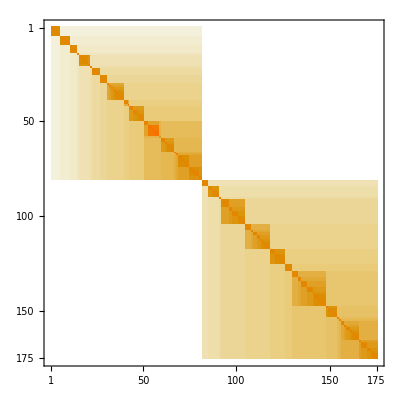

```mathematica
MatrixPlot[cleanmatrix[wribraw]]
```

```mathematica
allnamesinribtree = Drop[wribraw[[1]],1];
```

### Femur

```mathematica
femurtreeraw = Import["tree_femur_final.nex","Lines"];
```

```mathematica
femurtreess =StringSplit[femurtreeraw[[3]],"R]"|";"];
```

```mathematica
femurtree =StringJoin[StringDelete[femurtreess[[2]]," "],";"];
```

```mathematica
wfemurraw=PhylogeneticMatrices[femurtree][[1]];
```

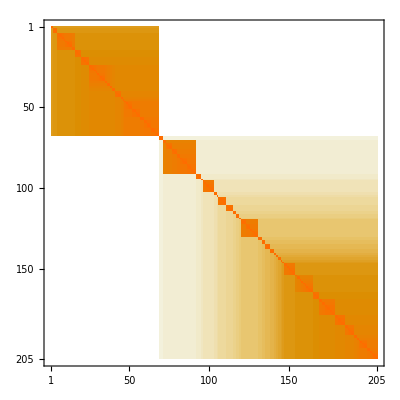

```mathematica
MatrixPlot[cleanmatrix[wfemurraw]]
```

```mathematica
allnamesinfemurtree = Drop[wfemurraw[[1]],1];
```

## Data with phylogeny

```mathematica
phyloadjustpts[{class1_,class2_,class3_}, tree_,plam_]:=
Module[{rawd,alldata,lens,indicator,names,namebyclass,datapts,databyclass,dtree,wmatraw,namesfromtree,wmat,
wmatdia,wmatoffdia,wwl,nwl,datpts,datanames,nameorder,indicatoradj,datptsinorder,datadj,datadjbyclass,namesinorderclass},
rawd = {class1,class2,class3};
alldata = Flatten[rawd,1];
lens = Map[Length,rawd];
indicator ={Join[Table[1,{lens[[1]]}],Table[0,{lens[[2]]}],Table[0,{lens[[3]]}]],Join[Table[0,{lens[[1]]}],Table[1,{lens[[2]]}],Table[0,{lens[[3]]}]],Join[Table[0,{lens[[1]]}],Table[0,{lens[[2]]}],Table[1,{lens[[3]]}]]};
names = alldata[[All,1]];
namebyclass = Table[Pick[names,indicator[[i]],1],{i,1,3}];
datapts = alldata[[All,{1,11,9}]];
databyclass = Table[Pick[datapts,indicator[[i]],1],{i,1,3}];
dtree = PruneTree[Flatten[databyclass[[All,All,1]]],tree];
wmatraw = PhylogeneticMatrices[dtree][[1]];
namesfromtree = Drop[wmatraw[[1]],1];
wmat = cleanmatrix[wmatraw];
(*nmat = makenmatrix[wmat];*)
{wmatdia, wmatoffdia}= matrix4lambda[wmat,1];
wwl = wmatdia + plam*wmatoffdia;
nwl = makenmatrix[wwl];
datpts= Flatten[databyclass[[All, All,{2,3}]],1];
datanames =  Flatten[databyclass[[All,All,1]],1];
nameorder = FindPermutation[datanames,namesfromtree];
indicatoradj = Map[Permute[#,nameorder]&,indicator];
datptsinorder = Permute[datpts,nameorder];
datadj = nwl.datptsinorder;
datadjbyclass = Table[Pick[datadj,indicatoradj[[i]],1],{i,1,3}];
namesinorderclass =  Table[Pick[namesfromtree,indicatoradj[[i]],1],{i,1,3}];
{datadjbyclass,namesinorderclass}
];
```

### Femur (new)

```mathematica
spinonames2 = {"Su","Ba","Sp"};
```

```mathematica
femurallraw  = Import["femur compactness all.csv"];
```

```mathematica
{Range[Length[femurallraw[[1]]]],femurallraw[[1]]}//TableForm
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
taxa | Reference | Specimen | Type of data | AFA | ALA | FAD | LAD | Global compactness | MD (mm) | MD log | Flying | Diving | finest.category | diving.or.not

```mathematica
femurallraw1 = Drop[femurallraw,1];
```

```mathematica
femurf0raw = Pick[femurallraw1,femurallraw1[[All,12]],0];
```

```mathematica
namesnotintree = Complement[femurf0raw[[All,1]],allnamesinfemurtree]
```

{Rhinoceros_unicornis}

```mathematica
badpos = Flatten[Map[Position[femurf0raw[[All,1]],#]&,namesnotintree],1]
```

{{112}}

```mathematica
femurf0raw1 = Delete[femurf0raw,badpos];
```

```mathematica
femurf0d0raw =  Pick[femurf0raw1,femurf0raw1[[All,13]],0];
```

```mathematica
femurf0d2raw =  Pick[femurf0raw1,femurf0raw1[[All,13]],2];
```

```mathematica
femurdinos = Pick[femurf0raw1,femurf0raw1[[All,13]],"UNKNOWN"];
```

```mathematica
fwdinosadj = phyloadjustpts[{femurf0d0raw,femurf0d2raw,femurdinos}, femurtree,0.06];
```

```mathematica
Position[fwdinosadj[[2,3]],"Spinosaurus_"]
```

{{17}}

```mathematica
Position[fwdinosadj[[2,3]],"Baryonyx"]
```

{{15}}

```mathematica
Position[fwdinosadj[[2,3]],"Suchomimus"]
```

{{16}}

```mathematica
spinonames2
```

{Su,Ba,Sp}

```mathematica
femurspinoadjpts = fwdinosadj[[1,3,{16,15,17}]]
```

{{1.47478,0.433565},{1.58328,0.631825},{1.30225,0.72605}}

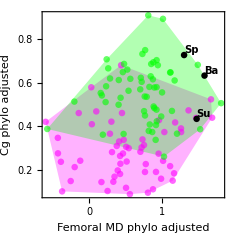

```mathematica
femuradjplot = Graphics[{
{Magenta,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[fwdinosadj[[1,1]]]]]}},
{Green,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[fwdinosadj[[1,2]]]]]}},
{Magenta,{Opacity[pointopacity],PointSize[.02],Map[Point,fwdinosadj[[1,1]]]}},
{Green,{Opacity[pointopacity],PointSize[.02],Map[Point,fwdinosadj[[1,2]]]}},
Table[{Black,PointSize[.02],Point[femurspinoadjpts[[k]]]},{k,1,Length[spinonames2]}],
Table[Text[Style[spinonames2[[k]],Black,10,Italic,Bold],femurspinoadjpts[[k]],{-1,-1}],{k,1,Length[spinonames2]}],
(*Text[Style["F0D2",10,"Arial",Bold,Italic],{Log[2],0.88},{0,0}],
Text[Style["F0D0",10,"Arial",Bold,Italic],{Log[50],0.45},{0,0}]*)
},AspectRatio->1,PlotRange-> All,PlotRangePadding-> Scaled[0.05],Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"A"]&}},FrameLabel-> {"Femoral MD phylo adjusted","Cg phylo adjusted"},FrameStyle-> Directive[Black,"Arial",10],ImageSize->mswordsize/2]
```

```mathematica
fm1 = Mean[fwdinosadj[[1,1]]]
```

{0.539852,0.29243}

```mathematica
fm2=Mean[fwdinosadj[[1,2]]]
```

{0.732264,0.555206}

```mathematica
femurrange =Map[MinMax,Transpose[Join[fwdinosadj[[1,1]],fwdinosadj[[1,2]]]]]
```

{{-0.602994,1.81182},{0.0883727,0.908312}}

```mathematica
frrat =(femurrange[[2,2]]-femurrange[[2,1]])/(femurrange[[1,2]]-femurrange[[1,1]])
```

0.339545

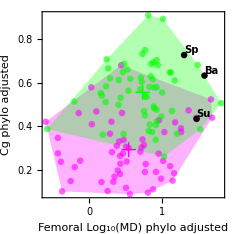

```mathematica
femuradjplot2 = Graphics[{
{Magenta,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[fwdinosadj[[1,1]]]]]}},
{Green,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[fwdinosadj[[1,2]]]]]}},
{Magenta,{Opacity[pointopacity],PointSize[.02],Map[Point,fwdinosadj[[1,1]]]}},
{Green,{Opacity[pointopacity],PointSize[.02],Map[Point,fwdinosadj[[1,2]]]}},
{Magenta,Thick, xlines2[fm1,0.1*{1,frrat}]},
{Green,Thick, xlines2[fm2,0.1*{1,frrat}]},
Table[{Black,PointSize[.02],Point[femurspinoadjpts[[k]]]},{k,1,Length[spinonames2]}],
Table[Text[Style[spinonames2[[k]],Black,10,Italic,Bold],femurspinoadjpts[[k]],{-1,-1}],{k,1,Length[spinonames2]}],
(*Text[Style["F0D2",10,"Arial",Bold,Italic],{Log[2],0.88},{0,0}],
Text[Style["F0D0",10,"Arial",Bold,Italic],{Log[50],0.45},{0,0}]*)
},AspectRatio->1,PlotRange-> All,PlotRangePadding-> Scaled[0.05],Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"A"]&}},FrameLabel-> {"Femoral Log_10(MD) phylo adjusted","Cg phylo adjusted"},FrameStyle-> Directive[Black,"Arial",10],ImageSize->mswordsize/2]
```

### Rib (new)

```mathematica
ribspinonames2 = {"Ba","Sp"};
```

```mathematica
riballraw  = Import["ribs compactness all.csv"];
```

```mathematica
riballraw1 = Drop[riballraw,1];
```

```mathematica
ribf0raw = Pick[riballraw1,riballraw1[[All,12]],0];
```

```mathematica
namesnotinribtree = Complement[ribf0raw[[All,1]],allnamesinribtree]
```

{Capra_aegagrus}

```mathematica
ribbadpos = Flatten[Map[Position[ribf0raw[[All,1]],#]&,namesnotinribtree],1]
```

{{76}}

```mathematica
ribf0raw1 = Delete[ribf0raw,ribbadpos];
```

```mathematica
ribf0d0raw =  Pick[ribf0raw1,ribf0raw1[[All,13]],0];
```

```mathematica
ribf0d2raw =  Pick[ribf0raw1,ribf0raw1[[All,13]],2];
```

```mathematica
ribdinos = Pick[ribf0raw1,ribf0raw1[[All,13]],"UNKNOWN"];
```

```mathematica
ribdinos
```

{{Lourinhanosaurus,Waskow & Mateus (2017),ML 370,,11,12,155.7,145,0.631,11.3,1.05308,0,UNKNOWN,none,0},{Saltriovenator,Dal Sasso et al. (2018),MSNM V3664,,4,5,196.5,189.6,0.704,21.3,1.32838,0,UNKNOWN,none,0},{Baryonyx,This study,BMNH 9951,Thin section,13,13,129.4,127,0.921,42.2,1.62531,0,UNKNOWN,UNKNOWN,UNKNOWN},{Spinosaurus,This study,FSAC-KK 11888,Thin section,14,14,100.5,93.9,0.931,35.1,1.54531,0,UNKNOWN,UNKNOWN,UNKNOWN},{Charcarodontosaurid,Cullen et al. (2020),MMCh PV 65,,14,15,100.5,89.8,0.805,25.5,1.40654,0,UNKNOWN,none,0},{Alamosaurus,Woodward (2005),HW-R2,,18,18,72.1,66,0.523,82.6,1.91698,0,UNKNOWN,none,0},{Plateosaurus,Klein & Sander (),SMNS F 29,Thin section,3,3,227,208.5,0.513,17.1,1.233,0,UNKNOWN,none,0},{Spinophorosaurus_nigerensis,Houssaye et al. (2016),Ni 5.40-7ax,,7,8,170.3,166.1,0.68,64.3,1.80821,0,UNKNOWN,none,0},{Apatosaurus_sp,Houssaye et al. (2016),BYU 145,,11,12,155.7,145,0.8,52.3,1.7185,0,UNKNOWN,none,0},{Diplodocus_sp,Houssaye et al. (2016),CMC 9932 ,,11,12,155.7,145,0.85,35,1.54407,0,UNKNOWN,none,0},{Brachiosaurus_sp,Houssaye et al. (2016),FMNH 25107,,11,12,155.7,145,0.84,95,1.97772,0,UNKNOWN,none,0},{Miragaia_longicollum,Houssaye et al. (2016),ML 433A ,,12,12,152.1,145,0.79,35,1.54407,0,UNKNOWN,none,0}}

```mathematica
rwdinosadj = phyloadjustpts[{ribf0d0raw,ribf0d2raw,ribdinos}, ribtree,0.07];
```

```mathematica
Position[rwdinosadj[[2,3]],"Spinosaurus"]
```

{{9}}

```mathematica
Position[rwdinosadj[[2,3]],"Baryonyx"]
```

{{8}}

```mathematica
Position[rwdinosadj[[2,3]],"Suchomimus"]
```

{}

```mathematica
ribspinonames2
```

{Ba,Sp}

```mathematica
ribspinoadjpts = rwdinosadj[[1,3,{8,9}]]
```

{{1.38577,0.754878},{1.30351,0.76516}}

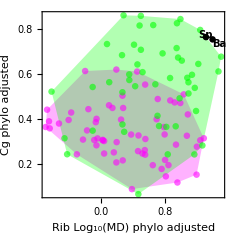

```mathematica
ribadjplot =Graphics[{
{Magenta,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[rwdinosadj[[1,1]]]]]}},
{Green,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[rwdinosadj[[1,2]]]]]}},
{Magenta,{Opacity[pointopacity],PointSize[.02],Map[Point,rwdinosadj[[1,1]]]}},
{Green,{Opacity[pointopacity],PointSize[.02],Map[Point,rwdinosadj[[1,2]]]}},
Table[{Black,PointSize[.02],Point[ribspinoadjpts[[k]]]},{k,1,Length[ribspinonames2]}],
Table[Text[Style[ribspinonames2[[k]],Black,10,Italic,Bold],ribspinoadjpts[[k]]+{{0,0},{0,.01}}[[k]],{{-1,1},{0,-1}}[[k]]],{k,1,Length[ribspinonames2]}]
(*Text[Style["F0D2",10,"Arial",Bold,Italic],{Log[2],0.88},{0,0}],
Text[Style["F0D0",10,"Arial",Bold,Italic],{Log[50],0.45},{0,0}]*)
},AspectRatio->1,PlotRange-> All,PlotRangePadding-> Scaled[0.05],Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"B"]&}},FrameLabel-> {"Rib Log_10(MD) phylo adjusted","Cg phylo adjusted"},FrameStyle-> Directive[Black,"Arial",10],ImageSize->mswordsize/2]
```

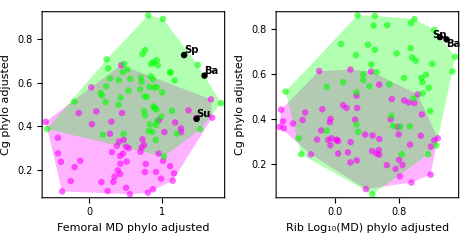

```mathematica
fig1xxplot = GraphicsGrid[{{femuradjplot,ribadjplot}},Spacings->0,ImageSize->mswordsize]
```

```mathematica
rm1 = Mean[rwdinosadj[[1,1]]]
```

{0.341513,0.343684}

```mathematica
rm2=Mean[rwdinosadj[[1,2]]]
```

{0.643651,0.557606}

```mathematica
ribrange =Map[MinMax,Transpose[Join[rwdinosadj[[1,1]],rwdinosadj[[1,2]]]]]
```

{{-0.6892,1.49241},{0.0655582,0.862263}}

```mathematica
rrrat =(ribrange[[2,2]]-ribrange[[2,1]])/(ribrange[[1,2]]-ribrange[[1,1]])
```

0.365191

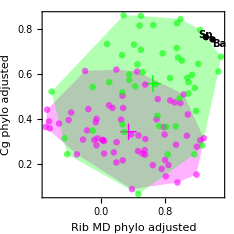

```mathematica
ribadjplot2 =Graphics[{
{Magenta,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[rwdinosadj[[1,1]]]]]}},
{Green,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[rwdinosadj[[1,2]]]]]}},
{Magenta,{Opacity[pointopacity],PointSize[.02],Map[Point,rwdinosadj[[1,1]]]}},
{Green,{Opacity[pointopacity],PointSize[.02],Map[Point,rwdinosadj[[1,2]]]}},
{Magenta,Thick, xlines2[rm1,0.1*{1,rrrat}]},
{Green,Thick, xlines2[rm2,0.1*{1,rrrat}]},
Table[{Black,PointSize[.02],Point[ribspinoadjpts[[k]]]},{k,1,Length[ribspinonames2]}],
Table[Text[Style[ribspinonames2[[k]],Black,10,Italic,Bold],ribspinoadjpts[[k]]+{{0,0},{0,.01}}[[k]],{{-1,1},{0,-1}}[[k]]],{k,1,Length[ribspinonames2]}],
(*Text[Style["F0D2",10,"Arial",Bold,Italic],{Log[2],0.88},{0,0}],
Text[Style["F0D0",10,"Arial",Bold,Italic],{Log[50],0.45},{0,0}]*)
},AspectRatio->1,PlotRange-> All,PlotRangePadding-> Scaled[0.05],Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"B"]&}},FrameLabel-> {"Rib MD phylo adjusted","Cg phylo adjusted"},FrameStyle-> Directive[Black,"Arial",10],ImageSize->mswordsize/2]
```

```mathematica
Sqrt[(rm1-rm2).(rm1-rm2)]
```

0.370203

```mathematica
StandardDeviation[Join[Map[# -rm1&,rwdinosadj[[1,1]]],Map[# -rm1&,rwdinosadj[[1,2]]]]]
```

{0.532597,0.186505}

```mathematica
femurf0d0andf0d2 = Join[femurf0d0raw,femurf0d2raw];
indicatorf0d0andf0d2 = {Join[Table[1,{Length[femurf0d0raw]}],Table[0,{Length[femurf0d2raw]}]],
Join[Table[0,{Length[femurf0d0raw]}],Table[1,{Length[femurf0d2raw]}]]};
femurf0d0andf0d2names =femurf0d0andf0d2[[All,1]];
femurnamesbyclass = Table[Pick[femurf0d0andf0d2names,indicatorf0d0andf0d2[[i]],1],{i,1,2}];
femurdata = femurf0d0andf0d2[[All,{1,11,9}]];
femurdatabyclass = Table[Pick[femurdata,indicatorf0d0andf0d2[[i]],1],{i,1,2}];
```

```mathematica
femursets2 = {femurdatabyclass[[1,All,{2,3}]],femurdatabyclass[[2,All,{2,3}]],fwdinosadj[[1,1]],fwdinosadj[[1,2]]};
```

```mathematica
DistributeDefinitions[femursets2,fwdinosadj]
```

{femursets2,fwdinosadj}

```mathematica
femursetnames2 = {"F0D0","F0D2","F0D0: lam = 0.06","F0D2, lam = 0.06"};
```

```mathematica
ribf0d0andf0d2 = Join[ribf0d0raw,ribf0d2raw];
indicatorf0d0andf0d2rib = {Join[Table[1,{Length[ribf0d0raw]}],Table[0,{Length[ribf0d2raw]}]],
Join[Table[0,{Length[ribf0d0raw]}],Table[1,{Length[ribf0d2raw]}]]};
ribf0d0andf0d2names =ribf0d0andf0d2[[All,1]];
ribdata = ribf0d0andf0d2[[All,{1,11,9}]];
ribnamesbyclass = Table[Pick[ribf0d0andf0d2names,indicatorf0d0andf0d2rib[[i]],1],{i,1,2}];
ribdatabyclass = Table[Pick[ribdata,indicatorf0d0andf0d2rib[[i]],1],{i,1,2}];
```

```mathematica
ribsets2 = {ribdatabyclass[[1,All,{2,3}]],ribdatabyclass[[2,All,{2,3}]],rwdinosadj[[1,1]],rwdinosadj[[1,2]]};
```

```mathematica
DistributeDefinitions[ribsets2]
```

{ribsets2}

```mathematica
ribsetnames2 = {"F0D0","F0D2","F0D0: lam = 0.07","F0D2, lam = 0.07"};
```

## Hopkins Statistic

This statistic is based on the difference between the distance from a real point to its nearest neighbor, U, and the distance from a randomly chosen point within the data space to the nearest real data point W

```mathematica
dist[p1_,p2_]:= Sqrt[(p1-p2).(p1-p2)];
```

```mathematica
Clear[hopkins,hopkinsch];
hopkins[pts_,frac_]:=
Module[{npts,ranges,randpts,ws,samp,nsamp,us,wsum,usum},
npts = Length[pts];
nsamp = Ceiling[npts*frac];
samp = RandomSample[pts,nsamp];
ranges = Map[MinMax,Transpose[samp]];
randpts = Transpose[Map[RandomReal[#,nsamp]&,ranges]];
ws =  Map[RankedMin[#,2]&,Outer[dist[#1,#2]&,samp,samp,1]];
us= Map[Min,Outer[dist[#1,#2]&,randpts,samp,1]];
wsum =Total[ws];
usum = Total[us];
usum/(wsum+usum)
];
```

```mathematica
hopkinsn[pts_,frac_,trials_]:=
Module[{npts,ranges,randpts,ws,samp,nsamp,us,wsum,usum,i,results},
npts = Length[pts];
nsamp = Ceiling[npts*frac];
results = Table[0,{trials}];
For[i=1,i<trials,i++,
samp = RandomSample[pts,nsamp];
ranges = Map[MinMax,Transpose[samp]];
randpts = Transpose[Map[RandomReal[#,nsamp]&,ranges]];
ws =  Map[RankedMin[#,2]&,Outer[dist[#1,#2]&,samp,samp,1]];
us= Map[Min,Outer[dist[#1,#2]&,randpts,samp,1]];
wsum =Total[ws];
usum = Total[us];
results[[i]] = usum/(wsum+usum)
];
Median[results]
];
```

```mathematica
lawsonjurs[pts_,frac_]:=
Module[{npts,ranges,randpts,ws,samp,nsamp,us,wsum,usum,xsel,ysel,rangef,xsandys},
npts = Length[pts];
nsamp = Ceiling[npts*frac];
samp = RandomSample[pts,nsamp];
ranges = Map[MinMax,Transpose[samp]];
xsandys = Transpose[pts];
xsel = Cases[xsandys[[1]],a_/;ranges[[1,1]]<= a <= ranges[[1,2]]];
ysel = Cases[xsandys[[2]],a_/;ranges[[2,1]]<= a <= ranges[[2,2]]];
randpts = Transpose[{RandomChoice[xsel,nsamp],RandomSample[ysel,nsamp]}];
ws =  Map[RankedMin[#,2]&,Outer[dist[#1,#2]&,samp,samp,1]];
us = Map[Min,Outer[dist[#1,#2]&,randpts,samp,1]];
wsum =Total[ws];
usum = Total[us];
usum/(wsum+usum)
];
```

```mathematica
hopkinschnew[pts_,frac_]:=
Module[{npts,range,randpts,ws,samp,nsamp,us,wsum,usum,reg,},
npts = Length[pts];
nsamp = Max[3,Ceiling[npts*frac]];
samp = RandomSample[pts,nsamp];
reg = ConvexHullRegion[samp];
randpts = RandomPoint[reg,nsamp];
ws =  Map[RankedMin[#,2]&,Outer[dist[#1,#2]&,samp,samp,1]];
us = Map[Min,Outer[dist[#1,#2]&,randpts,samp,1]];
wsum =Total[ws];
usum = Total[us];
usum/(wsum+usum)
];
```

```mathematica
hopkinsch[pts_,frac_]:=
Module[{npts,range,randpts,ws,samp,nsamp,us,wsum,usum,reg,regarea,boxarea,arearat,rmemf, rawrandpts,rawrandpts2,extracount,newpts,rawrand2,inregrandpts, inreglen,
missing,x2,newraw,newptslen},
npts = Length[pts];
nsamp = Max[3,Ceiling[npts*frac]];
samp = RandomSample[pts,nsamp];
range = Map[MinMax,Transpose[samp]];
reg = ConvexHullRegion[samp];
regarea = Area[reg];
boxarea = (range[[1,2]]-range[[1,1]])*(range[[2,2]]-range[[2,1]]);
arearat = 2*(boxarea/regarea);
extracount = Ceiling[nsamp*arearat];
rmemf = RegionMember[reg];
rawrandpts = Transpose[Map[RandomReal[#,extracount]&,range]];
inregrandpts = Select[rawrandpts,rmemf];
inreglen =  Length[inregrandpts];
missing = Max[0,nsamp-inreglen];
While[missing >0,
x2 = Max[Ceiling[missing*arearat],2*missing];
newraw =  Transpose[Map[RandomReal[#,x2]&,range]];
newpts = Select[ newraw,rmemf];
newptslen = Length[newpts];
inregrandpts = Join[inregrandpts,newpts];
missing =  Max[0,missing-newptslen];
];
If[Length[inregrandpts] == nsamp,
randpts = inregrandpts;
,
randpts = RandomSample[inregrandpts,nsamp];
];

ws =  Map[RankedMin[#,2]&,Outer[dist[#1,#2]&,samp,samp,1]];
us = Map[Min,Outer[dist[#1,#2]&,randpts,samp,1]];
wsum =Total[ws];
usum = Total[us];
usum/(wsum+usum)
];
```

```mathematica
makechrands[ptlist_]:=
Module[{npts,reg},
npts = Length[ptlist];
reg = ConvexHullRegion[ptlist];
RandomPoint[reg,npts]
];
```

```mathematica
makechrandsold[ptlist_]:=
Module[{npts,range,randpts,ws,samp,nsamp,us,wsum,usum,reg,regarea,boxarea,arearat,rmemf, rawrandpts,rawrandpts2,extracount,newpts,rawrand2,inregrandpts, inreglen,
missing,x2,newraw,newptslen},

nsamp = Length[ptlist];
range = Map[MinMax,Transpose[ptlist]];
reg = ConvexHullRegion[ptlist];
regarea = Area[reg];
boxarea = (range[[1,2]]-range[[1,1]])*(range[[2,2]]-range[[2,1]]);
arearat = 1.2*(boxarea/regarea);
extracount = Ceiling[nsamp*arearat];
rmemf = RegionMember[reg];
rawrandpts = Transpose[Map[RandomReal[#,extracount]&,range]];
inregrandpts = Select[rawrandpts,rmemf];
inreglen =  Length[inregrandpts];
missing = Max[0,nsamp-inreglen];
While[missing >0,
x2 = Max[Ceiling[missing*arearat],2*missing];
newraw =  Transpose[Map[RandomReal[#,x2]&,range]];
newpts = Select[ newraw,rmemf];
newptslen = Length[newpts];
inregrandpts = Join[inregrandpts,newpts];
missing =  Max[0,missing-newptslen];
];
If[Length[inregrandpts] == nsamp,
randpts = inregrandpts;
,
randpts = RandomSample[inregrandpts,nsamp];
];
randpts
];
```

```mathematica
hfrac = 0.2;
```

```mathematica
twosided[cdf_]:= 2*Min[cdf,1-cdf];
```

```mathematica
hoppvalue[dist_,x_]:= 
Module[{cdfv},
cdfv = CDF[dist,x];
2*Min[cdfv,1-cdfv]
];
```

```mathematica
makerandpts[count_,ranges_]:= Transpose[Map[RandomReal[#,count]&,ranges]];
```

```mathematica
unifpts[rang_,nn_,trials_]:=Table[ Transpose[Map[RandomReal[#,nn]&,rang]],{trials}];
```

```mathematica
Clear[hopkinstest]
```

```mathematica
hopkinstest[data_,hopfun_,frac_,nperset_,nsets_,ntrials_]:=
Module[{nulltrials,hs},
nulltrials = Flatten[ParallelTable[With[{testd = makechrandsold[data]},Table[hopfun[testd,frac],{nperset}]],{nsets}]];
hs = Mean[ParallelTable[hopfun[data,frac],{ntrials}]];
{hs,hoppvalue[EmpiricalDistribution[nulltrials],hs]}
];
```

```mathematica
DistributeDefinitions[makechrands,hoppvalue,hfrac,hopkinsch,hopkinschnew,lawsonjurs,hopkinsn,hopkins,dist]
```

{makechrands,hoppvalue,hfrac,hopkinsch,dist,hopkinschnew,lawsonjurs,hopkinsn,hopkins}

## Running Hopkins statistic tests

#### Hopkins null distribution

```mathematica
flens = Map[Length,femursets2]
```

{58,59,58,59}

```mathematica
rlens=Map[Length,ribsets2]
```

{62,49,62,49}

```mathematica
fptranges = Map[Map[MinMax,Transpose[#]]&,femursets2]
```

{{{-0.0357404,2.23553},{0.353,0.855}},{{-0.0136762,2.21864},{0.596,0.989}},{{-0.602994,1.68822},{0.0883727,0.679518}},{{-0.580445,1.81182},{0.260257,0.908312}}}

```mathematica
rptranges = Map[Map[MinMax,Transpose[#]]&,ribsets2]
```

{{{-0.378201,1.7439},{0.451,0.857}},{{-0.305395,1.89098},{0.436,0.998}},{{-0.6892,1.2773},{0.0879499,0.620511}},{{-0.615636,1.49241},{0.0655582,0.862263}}}

```mathematica
DistributeDefinitions[makerandpts,flens,fptranges,rlens,rptranges,femursets2,ribsets2]
```

{makerandpts,flens,fptranges,rlens,rptranges}

```mathematica
AbsoluteTiming[testtrials1 =  Flatten[ParallelTable[With[{testd = makechrandsold[femursets2[[1]]]},Table[hopkinsch[testd,hfrac],{100}]],{100}]];]
```

{13.1681,Null}

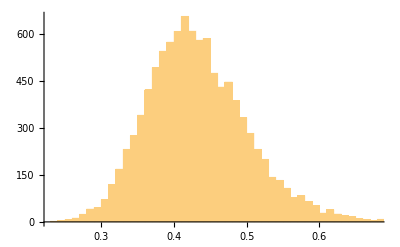

```mathematica
Histogram[testtrials1,{0.01}]
```

```mathematica
AbsoluteTiming[testtrials2 =   Flatten[ParallelTable[With[{testd = makechrandsold[femursets2[[1]]]},Table[hopkinsch[testd,hfrac],{10}]],{100}]];]
```

{1.75137,Null}

```mathematica
AbsoluteTiming[testtrials3 =   Flatten[ParallelTable[With[{testd = makechrandsold[femursets2[[1]]]},Table[hopkinsch[testd,hfrac],{20}]],{100}]];]
```

{3.29768,Null}

```mathematica
AbsoluteTiming[testtrials4=   Flatten[ParallelTable[With[{testd = makechrandsold[femursets2[[1]]]},Table[hopkinsch[testd,hfrac],{100}]],{20}]];]
```

{3.17818,Null}

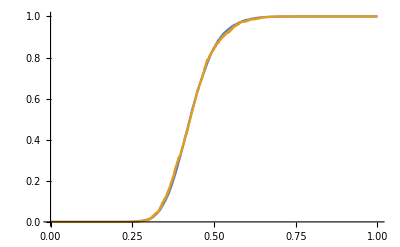

```mathematica
Plot[{CDF[EmpiricalDistribution[testtrials1],x],CDF[EmpiricalDistribution[testtrials2],x]},{x,0,1},PlotRange->All]
```

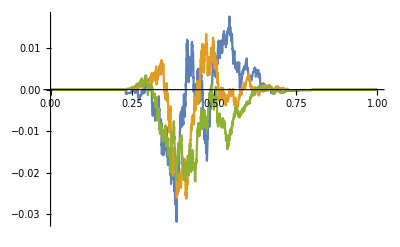

```mathematica
Plot[{CDF[EmpiricalDistribution[testtrials1],x]-CDF[EmpiricalDistribution[testtrials2],x],CDF[EmpiricalDistribution[testtrials1],x]-CDF[EmpiricalDistribution[testtrials3],x],CDF[EmpiricalDistribution[testtrials1],x]-CDF[EmpiricalDistribution[testtrials4],x]},{x,0,1},PlotRange->All]
```

### Femur data

```mathematica
AbsoluteTiming[femurhopkinsnulltrials = Map[Flatten,ParallelTable[With[{testd = makechrandsold[femursets2[[i]]]},Table[hopkins[testd,hfrac],{20}]],{i,1,Length[femursets2]},{100}]];]
```

{3.20565,Null}

```mathematica
Dimensions[femurhopkinsnulltrials]
```

{4,2000}

```mathematica
femurhopkinschnulltrials =  Map[Flatten,ParallelTable[With[{testd = makechrandsold[femursets2[[i]]]},Table[hopkinsch[testd,hfrac],{20}]],{i,1,Length[flens]},{100}]];
```

```mathematica
femurlawsonjursnulltrials =  Map[Flatten,ParallelTable[With[{testd = makechrandsold[femursets2[[i]]]},Table[lawsonjurs[testd,hfrac],{20}]],{i,1,Length[flens]},{100}]];
```

```mathematica
(*femureds =Map[EmpiricalDistribution[Flatten[#]]&,{femurhopkinsnulltrials,femurhopkinschnulltrials,femurlawsonjursnulltrials}];*)
```

```mathematica
femureds = Transpose[{Map[EmpiricalDistribution,femurhopkinsnulltrials],Map[EmpiricalDistribution,femurhopkinschnulltrials],Map[EmpiricalDistribution,femurlawsonjursnulltrials]}];
```

```mathematica
femurhds =Map[HistogramDistribution[Flatten[#],{0.01}]&,{femurhopkinsnulltrials,femurhopkinschnulltrials,femurlawsonjursnulltrials}];
```

```mathematica
Dimensions[femureds]
```

{4,3}

```mathematica
fs2len = Map[Length,femursets2]
```

{58,59,58,59}

```mathematica
betas = Map[BetaDistribution[#,#]&,fs2len]
```

{BetaDistribution[58,58],BetaDistribution[59,59],BetaDistribution[58,58],BetaDistribution[59,59]}

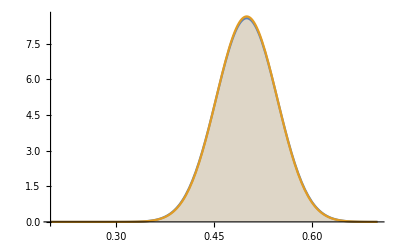

```mathematica
Plot[{PDF[betas[[1]],x],PDF[betas[[2]],x]},{x,0.2,0.7},PlotPoints->100,PlotRange->All,Filling->Axis,Exclusions->Null]
```

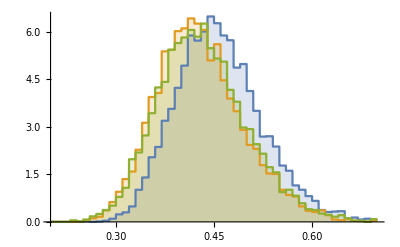

```mathematica
Plot[{PDF[femurhds[[1]],x],PDF[femurhds[[2]],x],PDF[femurhds[[3]],x]},{x,0.2,0.7},PlotPoints->100,PlotRange->All,Filling->Axis,Exclusions->Null]
```

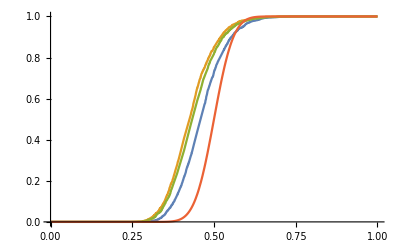

```mathematica
Plot[{CDF[femureds[[1,1]],x],CDF[femureds[[1,2]],x],CDF[femureds[[1,3]],x],CDF[betas[[1]],x]},{x,0,1},PlotRange->All]
```

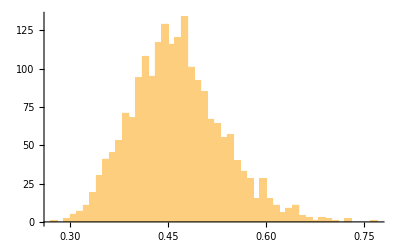

```mathematica
Histogram[femurhopkinsnulltrials[[1]],{.01}]
```

```mathematica
femurhopstats = ParallelMap[{hopkins[#,hfrac],hopkinsch[#,hfrac],lawsonjurs[#,hfrac]}&,femursets2]
```

{{0.430722,0.378569,0.363665},{0.436946,0.388325,0.549654},{0.528884,0.429321,0.48574},{0.451636,0.358688,0.364468}}

```mathematica
hoppvalue[femureds[[1,3]],femurhopstats[[1,3]]]
```

0.255

```mathematica
hopkinpvaluesfemur = Table[hoppvalue[femureds[[i,j]],femurhopstats[[i,j]]],{i,1,Length[femurhopstats]},{j,1,3}]
```

{{0.657,0.463,0.255},{0.906,0.591,0.083},{0.238,0.893,0.392},{0.866,0.264,0.29}}

```mathematica
ribhopstats = ParallelMap[{hopkins[#,hfrac],hopkinsch[#,hfrac],lawsonjurs[#,hfrac]}&,ribsets2]
```

{{0.508713,0.350807,0.357492},{0.442864,0.43867,0.349981},{0.411117,0.33242,0.411466},{0.412897,0.351833,0.27538}}

```mathematica
(*hopkinpvaluesrib = Table[hoppvalue[ribeds[[i,j]],ribhopstats[[i,j]]],{i,1,Length[ribhopstats]},{j,1,3}]*)
```

```mathematica
Map[Flatten,Transpose[{femursetnames2,hopkinpvaluesfemur}]]//TableForm
```

F0D0 | 0.657 | 0.463 | 0.255
F0D2 | 0.906 | 0.591 | 0.083
F0D0: lam = 0.06 | 0.238 | 0.893 | 0.392
F0D2, lam = 0.06 | 0.866 | 0.264 | 0.29

```mathematica
(*Map[Flatten,Transpose[{ribsetnames2,ribsrt,hopkinpvaluesrib}]]//TableForm*)
```

#### Running Hopkins multiple times

```mathematica
AbsoluteTiming[hptm = hopkinstest[femursets2[[1]],hopkins,0.2,100,100,100];]
```

{1.34537,Null}

```mathematica
hptm
```

{0.459051,0.9812}

#### Integrated test

```mathematica
AbsoluteTiming[hpt = hopkinstest[femursets2[[1]],hopkins,0.2,100,100,100];]
```

{1.34299,Null}

```mathematica
hpt
```

{0.439019,0.7904}

```mathematica
AbsoluteTiming[femurhoptests = Table[{hopkinstest[femursets2[[i]],hopkins,0.2,100,100,100],hopkinstest[femursets2[[i]],hopkinsch,0.2,100,100,100],hopkinstest[femursets2[[i]],lawsonjurs,0.2,100,100,100]},{i,1,Length[femursets2]}];]
```

{71.2409,Null}

```mathematica
AbsoluteTiming[ribhoptests = Table[{hopkinstest[ribsets2[[i]],hopkins,0.2,100,100,100],hopkinstest[ribsets2[[i]],hopkinsch,0.2,100,100,100],hopkinstest[ribsets2[[i]],lawsonjurs,0.2,100,100,100]},{i,1,Length[ribsets2]}];]
```

{71.3085,Null}

```mathematica
tabhead = {"Data set","H orig","p-value","H fpm","p-value","H lj","p-value"};
```

```mathematica
Join[{tabhead},Map[Flatten,Transpose[{femursetnames2,femurhoptests}]]]//TableForm
```

Data set | H orig | p-value | H fpm | p-value | H lj | p-value
F0D0 | 0.458255 | 0.9808 | 0.420539 | 0.9294 | 0.430249 | 0.965
F0D2 | 0.46248 | 0.7856 | 0.422928 | 0.9838 | 0.389685 | 0.6132
F0D0: lam = 0.06 | 0.466053 | 0.8446 | 0.434485 | 0.8752 | 0.416353 | 0.8202
F0D2, lam = 0.06 | 0.47156 | 0.855 | 0.417181 | 0.9494 | 0.385828 | 0.482

```mathematica
Join[{tabhead},Map[Flatten,Transpose[{ribsetnames2,ribhoptests}]]]//TableForm
```

Data set | H orig | p-value | H fpm | p-value | H lj | p-value
F0D0 | 0.468032 | 0.839 | 0.419393 | 0.9104 | 0.424185 | 0.9382
F0D2 | 0.447207 | 0.9264 | 0.413872 | 0.9928 | 0.402558 | 0.7922
F0D0: lam = 0.07 | 0.461528 | 0.971 | 0.420439 | 0.8848 | 0.429971 | 0.9266
F0D2, lam = 0.07 | 0.436974 | 0.9248 | 0.399996 | 0.8154 | 0.399177 | 0.7062

Data set | H orig | p-value | H fpm | p-value | H lj | p-value
F0D0 | 0.451856 | 0.9574 | 0.433715 | 0.9408 | 0.422553 | 0.9526
F0D2 | 0.451258 | 0.8676 | 0.412852 | 0.991 | 0.393713 | 0.6916
F0D0: lam = 0.07 | 0.465123 | 0.894 | 0.419089 | 0.8318 | 0.431866 | 0.872
F0D2, lam = 0.07 | 0.438332 | 0.929 | 0.404525 | 0.8898 | 0.400839 | 0.7232